## Finite Element examples from Paul Nylander (http://bugman123.com/Engineering/index.html):

SetDelayed::write: Tag Mean in Mean[x_] is Protected.

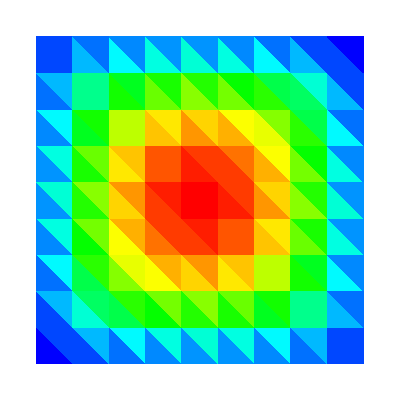

```mathematica
n=10;nodes=Flatten[Table[{x,y},{y,-1,1,2.0/(n-1)},{x,-1,1,2.0/(n-1)}],1];elems=Flatten[Table[i+{{0,1,n},{1,n+1,n}}+(j-1) n,{j,1,n-1},{i,1,n-1}],2];nnode=Length[nodes];nelem=Length[elems];
fixed=Map[Position[nodes,#][[1,1]]&,Select[nodes,Max[Abs[#]]==1&]];free=Complement[Range[nnode],fixed];
Kglobal=Table[0,{nnode},{nnode}];F=phi=Table[0,{nnode}];
Scan[(xy=Join[Transpose[nodes[[#]]],{{1,1,1}}];deta=Inverse[xy][[All,{1,2}]];Kglobal[[#,#]]+=Det[xy]deta.Transpose[deta]/2;F[[#]]+=Det[xy]/6)&,elems];
phi[[free]]=LinearSolve[Kglobal[[free,free]],F[[free]]];
Mean[x_]:=Plus@@x/Length[x];PlotColor[x_]:=Hue[2(1-x)/3];
Show[Graphics[Table[{PlotColor[Mean[phi[[elems[[i]]]]]/Max[phi]],Polygon[nodes[[elems[[i]]]]]},{i,1,nelem}],AspectRatio->1]]
```

### Interpolate the above plot:

```mathematica
n=275;x1=y1=-1;x2=y2=1;image=Table[0,{n},{n}];
xIntersect[{{x1_,y1_},{x2_,y2_}}]:=If[y1==y2,Infinity,x1+(y-y1)(x2-x1)/(y2-y1)];
Scan[(plist=nodes[[#]];xlist=nodes[[#,1]];ylist=nodes[[#,2]];p1=plist[[1]];{dx2,dy2}=plist[[2]]-p1;{dx3,dy3}=plist[[3]]-p1;Do[y=y1+(y2-y1)(i-1)/(n-1);{xa,xb,xc}=Map[xIntersect,Partition[Sort[plist,#1[[2]]<#2[[2]]&],2,1,1]];jlist=Round[n({xc,If[Abs[xb-xc]<Abs[xa-xc],xb,xa]}-x1)/(x2-x1)];If[jlist=!={},Do[x=x1+(x2-x1)(j-1)/(n-1);{xi,eta}=((x-p1[[1]]){dy3,-dy2}+(y-p1[[2]]){-dx3,dx2})/(dx2 dy3-dx3 dy2);image[[i,j]]=phi[[#]].{1-xi-eta,xi,eta},{j,Max[1,Min[jlist]],Min[n,Max[jlist]]}]],{i,Max[1,Round[n(Min[ylist]-y1)/(y2-y1)]],Min[n,Round[n(Max[ylist]-y1)/(y2-y1)]]}])&,elems];
ListDensityPlot[image,Mesh->False,Frame->False,ColorFunction->PlotColor,Epilog->Map[{Line[Map[({x,y}=nodes[[#,{1,2}]];n{(x-x1)/(x2-x1),(y-y1)/(y2-y1)})&,#]]}&,elems]]
```

-Graphics-

```mathematica
(*runtime:1.5 second*)n=36;dtheta=2Pi/n;nodes=Flatten[Table[r{Sin[theta],Cos[theta]},{r,1,2,0.25},{theta,0,2Pi-dtheta,dtheta}],1];
elems=Flatten[Table[n j+Append[Table[i+{0,1,n+1,n},{i,1,n-1}],{1,n+1,2n,n}],{j,0,3}],1];nnode=Length[nodes];nelem=Length[elems];
i=3n/2+1;fixed={{i-1,"x"},{i,"x"},{i,"y"},{i+1,"x"}};loads={{n+1,{0,-200}}};
Dkl:=0.25{{-1+y,1-y,1+y,-1-y},{-1+x,-1-x,1+x,1-x}};Dkm=0.25{{-1,1,1,-1},{-1,-1,1,1}};
e=1500;nu=0.3;Epss={{1,nu,0},{nu,1,0},{0,0,(1-nu)/2}}e/(1-nu^2);thk=1;
Kglobal=Table[0,{2nnode},{2nnode}];
Scan[(element=#;enodes=nodes[[element]];Klocal=Table[0,{8},{8}];Kee=Table[0,{4},{4}];Kre=Table[0,{8},{4}];Scan[({x,y}=#/Sqrt[3];t=Inverse[Dkl.enodes].Dkl;strain={{t[[1,1]],0,t[[1,2]],0,t[[1,3]],0,t[[1,4]],0},{0,t[[2,1]],0,t[[2,2]],0,t[[2,3]],0,t[[2,4]]},{t[[2,1]],t[[1,1]],t[[2,2]],t[[1,2]],t[[2,3]],t[[1,3]],t[[2,4]],t[[1,4]]}};ttm=-2Inverse[Dkm.enodes].{{x,0},{0,y}};ct={{ttm[[1,1]],0,ttm[[1,2]],0},{0,ttm[[2,1]],0,ttm[[2,2]]},{ttm[[2,1]],ttm[[1,1]],ttm[[2,2]],ttm[[1,2]]}}Det[Dkm.enodes]/Det[Dkl.enodes];Dj=thk Abs[Det[Dkl.enodes]];Klocal+=Transpose[strain].(Epss.strain) Dj;Kee+=Transpose[ct].(Epss.ct) Dj;Kre+=Transpose[strain].(Epss.ct) Dj)&,{{-1,-1},{1,-1},{1,1},{-1,1}}];Klocal-=Kre.Inverse[Kee].Transpose[Kre];Do[Kglobal[[2element[[i]]-di,2element[[j]]-dj]]+=Klocal[[2i-di,2j-dj]],{di,0,1},{dj,0,1},{i,1,4},{j,1,4}])&,elems];
Scan[(i=2#[[1]]-If[#[[2]]=="x",1,0];Kglobal[[i,i]]*=10^6)&,fixed];
paload=Table[0,{2nnode}];Scan[(paload[[2#[[1]]-{1,0}]]=#[[2]])&,loads];
del=Partition[LinearSolve[Kglobal,paload],2];
Do[nodes2=nodes+scale del;Show[Graphics[Map[Line[nodes2[[#]]]&,elems],AspectRatio->Automatic]],{scale,0,1,0.1}];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {« 1 »} may contain significant numerical errors.

```mathematica
x0=299.2239;h=625.0925;a=118.6261;n=20;EA=25000.0;
nodes=Flatten[Table[z=a(Cosh[x0/a]-Cosh[x/a]);r=54-37z/h;Table[{x,0,z}+r{-Tanh[x/a]Cos[theta],Sin[theta],-Sech[x/a]Cos[theta]},{theta,0,4Pi/3,2Pi/3}],{x,-x0,x0,2x0/n}],1];
elems=Flatten[Table[Join[{{1,2},{2,3},{3,1}},If[i<n,{{1,4},{2,5},{3,6},{1,5},{2,6},{3,4}},{}]]+3i,{i,0,n}],1];
fixed=Join[{1,2,3},nnode-{2,1,0}];nnode=Length[nodes];nelem=Length[elems];nfixed=Length[fixed];free=Complement[Range[nnode],fixed];
A=Map[({i1,i2}=#;del=nodes[[i2]]-nodes[[i1]];del/=del.del;Flatten[Table[If[i==i1,-1,If[i==i2,1,0]]del,{i,1,nnode}][[free]]])&,elems];
Kglobal=EA Transpose[A].A;
Q=Table[{0,0,0},{nnode}];Q[[Ceiling[nnode/2]]]={0,1,0};
q=Table[{0,0,0},{nnode}];q[[free]]=Partition[LinearSolve[Kglobal,Flatten[Q[[free]]]],3];
e=Map[({i1,i2}=#;q[[i1]]-q[[i2]])&,elems];s=Map[Sqrt[#.#]&,e];smax=Max[s];
Do[Show[Graphics3D[Table[elem=elems[[i]];{Hue[2(1-scale s[[i]]/smax)/3],Line[nodes[[elem]]+scale q[[elem]]]},{i,1,nelem}]]],{scale,0,1,0.1}];
```

```mathematica
LinearSolve[A_,x_]:=Module[{n=Length[A],i=1,j=1,imax,B},B=Table[Append[A[[i]],x[[i]]],{i,1,n}];While[i≤n&&j≤n+1,imax=i;Do[If[Abs[B[[k,j]]]>Abs[B[[imax,j]]],imax=k],{k,i+1,n}];If[B[[imax,j]]≠0.0,{B[[i]],B[[imax]]}={B[[imax]],B[[i]]};B[[i]]/=B[[i,j]];Do[B[[u]]-=B[[u,j]] B[[i]],{u,i+1,n}];i++];j++];Do[B[[i,n+1]]=(B[[i,n+1]]-Sum[B[[i,j]]B[[j,n+1]],{j,i+1,n}])/B[[i,i]],{i,n-1,1,-1}];B[[All,n+1]]];
```

SetDelayed::write: Tag LinearSolve in LinearSolve[A_, x_] is Protected.